# End Term Project

## Music Genre Classification

## Submitted by : Shubbham Gupta Student Id: 19205033

## Introduction:

### Music Genre Classification

Music genre classification is the classification of the music audios on the basis of their genres, for example, blues, classical, hip-hop, etc. Music genre is generally needed with the music apps where the app can suggest other songs based on the genres of the songs a user listen. These suggestions not only help the user to find similar genre songs but also reduces the searching load and hence provide efficiency. Music audio is a type of continuous signal. Music audios can exist in any format like, .mp3, .wav, etc.

Music classification is very trending among companies to predict recommendations for their customers. Determining music genres is very first step in classification. Machine learning techniques have been successful in extracting patterns from large dataset and classifying. It can be implemented in Music Analysis also.
In the project we will be analyzing an audio signal and extracting properties which will be used to determine genre of that signal. Then it will be classified into different genres.

### Dataset

Here, we have used the GTZAN dataset for the training of the model. Even though the dataset is considered ‘standard’ in music genre classification problem, it has a few flaws, which quite significantly impact the interpretation of the results of any model trained on the GTZAN. In fact, there is even a paper describing in details all the cons of the GTZAN dataset. Some of the problems described there are misclassification, distortions and duplicates in the data.
The following genres are given in the data:

Blues

Classical

Disco

Hip-Hop

Pop

Country

Jazz

Rock

Metal

Reggae

Another problem with GTZAN is related not to its construction itself, but the fact that it was made in 2000. Though some may argue, it is quite commonly accepted truth, that during the last 16 years, there actually was some contribution to the musical world overall, particularly to the electronic music. GTZAN doesn't reflect this contribution - in fact it doesn't recognize electronic music as a genre at all, which may seem pretty odd nowadays.
The dataset is noisy as two or more genres will show similar frequency and other properties which will be used by the model. For example, Genre Blue and Country are alike, similarly, Hip hop and Pop are similar.
The dataset used here is GTZAN Dataset, of which, all 10 genres have been used in this project. Each genre contains 100 music files, which belong to a particular genre, and each file's length is of 30 seconds.

### Music Features used

These are the features which were extracted from the raw audio signal.

• Zero Crossing Rate (ZCR): A zero crossing point refers to one where the signal changes sign from positive to negative. The entire signal is divided into smaller frames, and the number of zero-crossings present in each frame are determined. The frame length is chosen to be 2048 points with a hop size of 512 points. Note that these frame parameters have been used consistently across all features discussed in this section. Finally, the average and standard deviation of the ZCR across all frames are chosen as representative features.
 • Spectral Roll-off: This feature corresponds to the value of frequency below which 85% (this threshold can be defined by the user) of the total energy in the spectrum lies.
 •  Spectral Centroid: For each frame, this corresponds to the frequency around which most of the energy is centered 
 • Loudness: It measures an estimated loudness measure at each band . The loudness property uses Stevens’s power law, computed using power^0.67.
 • Spectral Contrast: Each frame is divided into a pre-specified number of frequency bands. And, within each frequency band, the spectral contrast is calculated as the difference between the maximum and minimum magnitudes
  • Mel-Frequency Cepstral Coefficients (MFCC): MFCCs[5] have been very useful features for tasks such as speech recognition. First, the Short-Time Fourier-Transform (STFT) of the signal is taken with n_fft=2048 and hop_size=512 and a Hann window. Next, we compute the power spectrum and then apply the triangular MEL filter bank, which mimics the human perception of sound. This is followed by taking the discrete cosine transform of the logarithm of all filter-bank energies, thereby obtaining the MFCCs. The parameter n_mels, which corresponds to the number of filter banks, was set to 13 in this study.
   
For each of the features described above, the mean and standard deviation of the values taken across frames is considered as the representative final feature that is fed to the model. The features described in this section would be used to train machine learning algorithms.

### Classifiers

This section provides a brief overview of the seven machine learning classifiers adopted in this study

#### Decision Tree

Decision trees are a rather singular class of classifiers: we would like to construct an optimal tree, the nodes consist of question on the input vector. Progressing through the nodes by answering the questions, we eventually reach a leaf, which corresponds to a prediction on the class of the input. An example for a different problem can be seen below.
Building an optimal decision tree can be very costly, because of the exponential nature of the space. However, efficient algorithms have been designed to create very effective trees. 
Decision tree are not very useful when data is noisy or redundant.

#### Gradient Boosted Trees

Gradient Boosting is similar to AdaBoost in that they both use an ensemble of decision trees to predict a target label. However, unlike AdaBoost, the Gradient Boost trees have a depth larger than 1. In practice, we’ll typically see Gradient Boost being used with a maximum number of leaves of between 8 and 32.
Gradient Boosting trains many models in a gradual, additive and sequential manner. Gradient boosting identifies the shortcomings of weak learner i.e decision trees by using gradients in the loss function. The loss function is a measure indicating how good are model’s coefficients are at fitting the underlying data. A logical understanding of loss function would depend on what we are trying to optimise. One of the biggest motivations of using gradient boosting is that it allows one to optimise a user specified cost function, instead of a loss function that usually offers less control and does not essentially correspond with real world applications.

#### Linear Regression

Linear regression is used for finding linear relationship between target and one or more predictors. There are two types of linear regression- Simple and Multiple. In this model we have used multiple linear regression. Linear regression can only be used when one has two continuous variables—an independent variable and a dependent variable. The independent variable is the parameter that is used to calculate the dependent variable or outcome. A multiple regression model extends to several explanatory variables.
Multiple linear regression (MLR), also known simply as multiple regression, is a statistical technique that uses several explanatory variables to predict the outcome of a response variable. The goal of multiple linear regression (MLR) is to model the linear relationship between the explanatory (independent) variables and response (dependent) variable.

The formula  for multiple linear regression is
y_i=β_0+β_1 x_(1i)+β_2 x_(2i)+β_3 x_(3i)....................+β_n x_ni + ϵ
where, for i=n observations:
y_i ​= dependent variable
x_i​ = independent variables
β_0 ​= y-intercept (constant)
β_p​ = slope coefficients for each independent variable
ϵ = the model’s error (also known as the residuals)​

#### K-Nearest Neighbors

This approach is the widely used technique of K-Nearest Neighbors. This is often one of the first techniques applied to classification problems because of its accessibility of implementation. The idea here is to “place” our training set in space, coloring each example using our labels, pick k, and then find the k “nearest” neighbors of the testing example that we are trying to classify. We then make our prediction as the most represented class amongst the neighbors. 
The parameters in this model are the distance function, and k. The latter is chosen by training on different values of k, and picking the best one. The distance is often chosen to be the euclidean distance
 			D_(x_1,x_2)=√((x_(1_1)-x_(2_1))^2+(x_(1_2)-x_(2_2))^2+(x_(1_3)-x_(2_3))^2......(x_(1_n)-x_(2_n))^2)

#### Neural Network

Our next approach was the use of Neural Networks. They are very prone to customization, and considering our approach of a rather peculiar feature vector with a rather small data set, this method seemed to be a good choice. The idea is to give our network several inputs (each input is a single feature). Then, we navigate through the network by applying weights to our inputs, summing them, and finally using an activation function to obtain the subsequent nodes. This process is repeated multiple times through the hidden layers, before applying a final activation function to obtain the output layer, our prediction. 
The training takes place on the weights, which are initialized randomly. They are updated by trying to minimize training error using gradient descent, and are used after the training period to try and make predictions. In our case, we used the softmax function as our final activation function.

#### Random Forest

Random Forest is an ensemble learner that combines the prediction from a pre-specified number of decision trees. It works on the integration of two main principles: 
1) each decision tree is trained with only a subset of the training samples which is known as bootstrap aggregation, 
2) each decision tree is required to make its prediction using only a random subset of the features. 
The final predicted class of the RF is determined based on the majority vote from the individual classifiers.

#### Gaussian Process

Gaussian process regression (GPR) is a nonparametric, Bayesian approach to regression that is making waves in the area of machine learning. GPR has several benefits, working well on small datasets and having the ability to provide uncertainty measurements on the predictions. Unlike many popular supervised machine learning algorithms that learn exact values for every parameter in a function, the Bayesian approach infers a probability distribution over all possible values. Let’s assume a linear function: y=wx+ϵ.
Gaussian process regression is nonparametric (i.e. not limited by a functional form), so rather than calculating the probability distribution of parameters of a specific function, GPR calculates the probability distribution over all admissible functions that fit the data. However, we specify a prior (on the function space), calculate the posterior using the training data, and compute the predictive posterior distribution on our points of interest. 
y~GP(m(x),k(x,x`)+δ_ij σ_n^2)

## Functions

Pure function methods are used to create the following functions rather than normal function method as the number of arguments passed are not defined thus making it easier to call the function later. In some functions Blocks are used instead of Modules due to the support of Dynamic scoping in Blocks

### MusicConvert

The following function MusicConvert  is used to extract various properties of an audio signal. The properties extracted are Zero crossing rate, Spectral Centroid, Spectral Roll Off, Loudness, Minimum and Maximum amplitude, MFCCs values. These are used to know each signal and understand relation of genre with these properties. This function takes one argument which is audio format of the file.

```mathematica
MusicConvert=(AudioLocalMeasurements[#,{"ZeroCrossingRate","SpectralCentroid","SpectralRollOff","Loudness","MinMax","MFCC"},"Association"])&;
```

### MusicDataset

The following function MusicDataset takes properties from above mentioned function and saved them in a list as a form of Association so that later it can be converted into dataset.
This function takes two arguments which are the genre type as string and an integer to map the string.

```mathematica
MusicDataset=(                                                                          (*Alter the SetDirectory to the location where genres folder will be stored*)
Block[{x=#1,y=#2},SetDirectory[StringJoin["/media/shubbham28/New Volume/UCD/Mathematica for Research/Project/genres/",x]];
files=FileNames[];(*It will take filenames of the folder into a list form and Do will run for each file *)
Do[X=MusicConvert[Audio[File[StringJoin["/media/shubbham28/New Volume/UCD/Mathematica for Research/Project/genres/",x,"/",files[[i]]]]]];(*list is the location where each time association will be added*)
AppendTo[list,<|{"mean_ZCR"-> Mean[X["ZeroCrossingRate"]["Values"]],"std_ZCR"-> StandardDeviation[X["ZeroCrossingRate"]["Values"]],"mean_SCEN"-> Mean[X["SpectralCentroid"]["Values"]],"std_SCEN"-> StandardDeviation[X["SpectralCentroid"]["Values"]],"mean_SRO"-> Mean[X["SpectralRollOff"]["Values"]],"std_SRO"-> StandardDeviation[X["SpectralRollOff"]["Values"]],"mean_LOUD"-> Mean[X["Loudness"]["Values"]],"std_LOUD"-> StandardDeviation[X["Loudness"]["Values"]],"mean_SCON"-> Mean[X["MinMax"]["Values"][[All,2]]-X["MinMax"]["Values"][[All,1]]],"std_SCON"-> StandardDeviation[X["MinMax"]["Values"][[All,2]]-X["MinMax"]["Values"][[All,1]]],"mean_MFCC1"-> Mean[X["MFCC"]["Values"][[All,1]]],"std_MFCC1"-> StandardDeviation[X["MFCC"]["Values"][[All,1]]],"mean_MFCC2"-> Mean[X["MFCC"]["Values"][[All,2]]],"std_MFCC2"-> StandardDeviation[X["MFCC"]["Values"][[All,2]]],"mean_MFCC3"-> Mean[X["MFCC"]["Values"][[All,3]]],"std_MFCC3"-> StandardDeviation[X["MFCC"]["Values"][[All,3]]],"mean_MFCC4"-> Mean[X["MFCC"]["Values"][[All,4]]],"std_MFCC4"-> StandardDeviation[X["MFCC"]["Values"][[All,4]]],"mean_MFCC5"-> Mean[X["MFCC"]["Values"][[All,5]]],"std_MFCC5"-> StandardDeviation[X["MFCC"]["Values"][[All,5]]],
"mean_MFCC6"-> Mean[X["MFCC"]["Values"][[All,6]]],"std_MFCC6"-> StandardDeviation[X["MFCC"]["Values"][[All,6]]],"mean_MFCC7"-> Mean[X["MFCC"]["Values"][[All,7]]],"std_MFCC7"-> StandardDeviation[X["MFCC"]["Values"][[All,7]]],"mean_MFCC8"-> Mean[X["MFCC"]["Values"][[All,8]]],"std_MFCC8"-> StandardDeviation[X["MFCC"]["Values"][[All,8]]],"mean_MFCC9"-> Mean[X["MFCC"]["Values"][[All,9]]],"std_MFCC9"-> StandardDeviation[X["MFCC"]["Values"][[All,9]]],"mean_MFCC10"-> Mean[X["MFCC"]["Values"][[All,10]]],"std_MFCC10"-> StandardDeviation[X["MFCC"]["Values"][[All,10]]],"mean_MFCC11"-> Mean[X["MFCC"]["Values"][[All,11]]],"std_MFCC11"-> StandardDeviation[X["MFCC"]["Values"][[All,11]]],"mean_MFCC12"-> Mean[X["MFCC"]["Values"][[All,12]]],"std_MFCC12"-> StandardDeviation[X["MFCC"]["Values"][[All,12]]],"mean_MFCC13"-> Mean[X["MFCC"]["Values"][[All,13]]],"std_MFCC13"-> StandardDeviation[X["MFCC"]["Values"][[All,13]]],"Genre"-> y}|>];,{i,1,Length[files],1}];])&;
```

### GenePredict

The following  function GenrePredict  forms 7 types of prediction model each based on different methods. It is done to compare the efficiency of different methods. This function takes one argument of dataset on which the model has to be trained in it.
Here default method of Predict is not used which shows the best method directly, to show difference between each method.

```mathematica
GenrePredict=({Predict[#1->"Genre",Method->"DecisionTree"],Predict[#1->"Genre",Method->"GradientBoostedTrees"],Predict[#1->"Genre",Method->"LinearRegression"],Predict[#1->"Genre",Method->"NearestNeighbors"],Predict[#1->"Genre",Method->"NeuralNetwork"],Predict[#1->"Genre",Method->"RandomForest"],Predict[#1->"Genre",Method->"GaussianProcess"]})&;
```

### ResultModel

The following function ResultModel use the function GenrePredict to train model and then save them in a list as a Association to made a final dataset which contain accuracy of each predictor model. This function has 4 arguments  which are training dataset, testing dataset, integer denoting genres taken and list of genres removed from original dataset

```mathematica
ResultModel=(Block[{d=#1,r=#2,g=#3,re=#4},{pdt,pgb,plr,pnn,pne,prf,pgp}=GenrePredict[d];
(*res is the location where each time association will be added*)
AppendTo[res,N[<|"Genre"-> g,"Removed"-> re,"DecisionTree"-> Count[Normal[#2[[All,"Genre"]]]-Round[ pdt[#2]],0]/Length[r],"GradientBoostedTrees"-> Count[Normal[#2[[All,"Genre"]]]-Round[ pgb[#2]],0]/Length[r],"LinearRegression"-> Count[Normal[#2[[All,"Genre"]]]-Round[ plr[#2]],0]/Length[r],"NearestNeighbors"-> Count[Normal[#2[[All,"Genre"]]]-Round[ pnn[#2]],0]/Length[r],"NeuralNetwork"-> Count[Normal[#2[[All,"Genre"]]]-Round[ pne[#2]],0]/Length[r],"RandomForest"-> Count[Normal[#2[[All,"Genre"]]]-Round[ prf[#2]],0]/Length[r],"GaussianProcess"-> Count[Normal[#2[[All,"Genre"]]]-Round[ pgp[#2]],0]/Length[r]|>]];])&;
```

### PredictGenre

The following function PredictGenre  will predict the genre out of the ten genres taken from the dataset. It takes one argument which is  the File-path of the audio whose genre is to be predicted. It uses all ten genres to create three different predictor models and then give a single answer by taking average of the result. It gives a predicted genre of the input along with audio and AudioPlot of the input

```mathematica
PredictGenre=(
X=MusicConvert[Audio[File[#]]];
PRG=<|{"mean_ZCR"-> Mean[X["ZeroCrossingRate"]["Values"]],"std_ZCR"-> StandardDeviation[X["ZeroCrossingRate"]["Values"]],"mean_SCEN"-> Mean[X["SpectralCentroid"]["Values"]],"std_SCEN"-> StandardDeviation[X["SpectralCentroid"]["Values"]],"mean_SRO"-> Mean[X["SpectralRollOff"]["Values"]],"std_SRO"-> StandardDeviation[X["SpectralRollOff"]["Values"]],"mean_LOUD"-> Mean[X["Loudness"]["Values"]],"std_LOUD"-> StandardDeviation[X["Loudness"]["Values"]],"mean_SCON"-> Mean[X["MinMax"]["Values"][[All,2]]-X["MinMax"]["Values"][[All,1]]],"std_SCON"-> StandardDeviation[X["MinMax"]["Values"][[All,2]]-X["MinMax"]["Values"][[All,1]]],"mean_MFCC1"-> Mean[X["MFCC"]["Values"][[All,1]]],"std_MFCC1"-> StandardDeviation[X["MFCC"]["Values"][[All,1]]],"mean_MFCC2"-> Mean[X["MFCC"]["Values"][[All,2]]],"std_MFCC2"-> StandardDeviation[X["MFCC"]["Values"][[All,2]]],"mean_MFCC3"-> Mean[X["MFCC"]["Values"][[All,3]]],"std_MFCC3"-> StandardDeviation[X["MFCC"]["Values"][[All,3]]],"mean_MFCC4"-> Mean[X["MFCC"]["Values"][[All,4]]],"std_MFCC4"-> StandardDeviation[X["MFCC"]["Values"][[All,4]]],"mean_MFCC5"-> Mean[X["MFCC"]["Values"][[All,5]]],"std_MFCC5"-> StandardDeviation[X["MFCC"]["Values"][[All,5]]],
"mean_MFCC6"-> Mean[X["MFCC"]["Values"][[All,6]]],"std_MFCC6"-> StandardDeviation[X["MFCC"]["Values"][[All,6]]],"mean_MFCC7"-> Mean[X["MFCC"]["Values"][[All,7]]],"std_MFCC7"-> StandardDeviation[X["MFCC"]["Values"][[All,7]]],"mean_MFCC8"-> Mean[X["MFCC"]["Values"][[All,8]]],"std_MFCC8"-> StandardDeviation[X["MFCC"]["Values"][[All,8]]],"mean_MFCC9"-> Mean[X["MFCC"]["Values"][[All,9]]],"std_MFCC9"-> StandardDeviation[X["MFCC"]["Values"][[All,9]]],"mean_MFCC10"-> Mean[X["MFCC"]["Values"][[All,10]]],"std_MFCC10"-> StandardDeviation[X["MFCC"]["Values"][[All,10]]],"mean_MFCC11"-> Mean[X["MFCC"]["Values"][[All,11]]],"std_MFCC11"-> StandardDeviation[X["MFCC"]["Values"][[All,11]]],"mean_MFCC12"-> Mean[X["MFCC"]["Values"][[All,12]]],"std_MFCC12"-> StandardDeviation[X["MFCC"]["Values"][[All,12]]],"mean_MFCC13"-> Mean[X["MFCC"]["Values"][[All,13]]],"std_MFCC13"-> StandardDeviation[X["MFCC"]["Values"][[All,13]]]}|>;
d=original;
p1=Predict[d->"Genre",Method->BestPred[[1]]];
p2=Predict[d->"Genre",Method->BestPred[[2]]];
p3=Predict[d->"Genre",Method->BestPred[[3]]];
resgen=Switch[Normal[Round[Mean[{p1[PRG],p2[PRG],p3[PRG]}]]],1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
Print[Audio[File[#]]];
Print[Style[resgen,Bold]," is the best predicted Genre of the given audio file"];
AudioPlot[Audio[File[#]]]
)&;
```

## Data Processing

### Data Formation

The following statements create a list for saving properties of audio and the converting it to dataset original. MusicDataset is called 10 times to create a dataset of 1000 rows having 100 rows of each genre. Later  list is changed to dataset for prediction.

```mathematica
list={};                                                   (*Same variable which is used in MusicDataset. Change at both places if change is needed*)
MusicDataset["blues",1]
MusicDataset["classical",2]
MusicDataset["disco",3]
MusicDataset["hiphop",4]
MusicDataset["pop",5]                              (*Music Dataset is executed for all 10 genres to make the main dataset, *)
MusicDataset["country",6]                      (*it will be sliced according to the need later*)
MusicDataset["jazz",7]    
MusicDataset["rock",8]
MusicDataset["metal",9]
MusicDataset["reggae",10]
original=Dataset[list];                                   (*From Association to Dataset*)
```

The following two commands are added to export the dataset formed after getting AudioLocalMeasurements to a csv file and import the same dataset into the original to continue the process.

#### Export["/media/shubbham28/New Volume/UCD/Mathematica for Research/Project/dataset.csv", original]; original = Import["/media/shubbham28/New Volume/UCD/Mathematica for Research/Project/dataset.csv", "Dataset", "HeaderLines" -> 1];

```mathematica
res={};                                                                      (*Same variable which will be used in Result Model which will collect predictions*)
original[[1;;10,All]]                         (*Showing just the head of how original dataset looks*)
```

Dataset[<>]

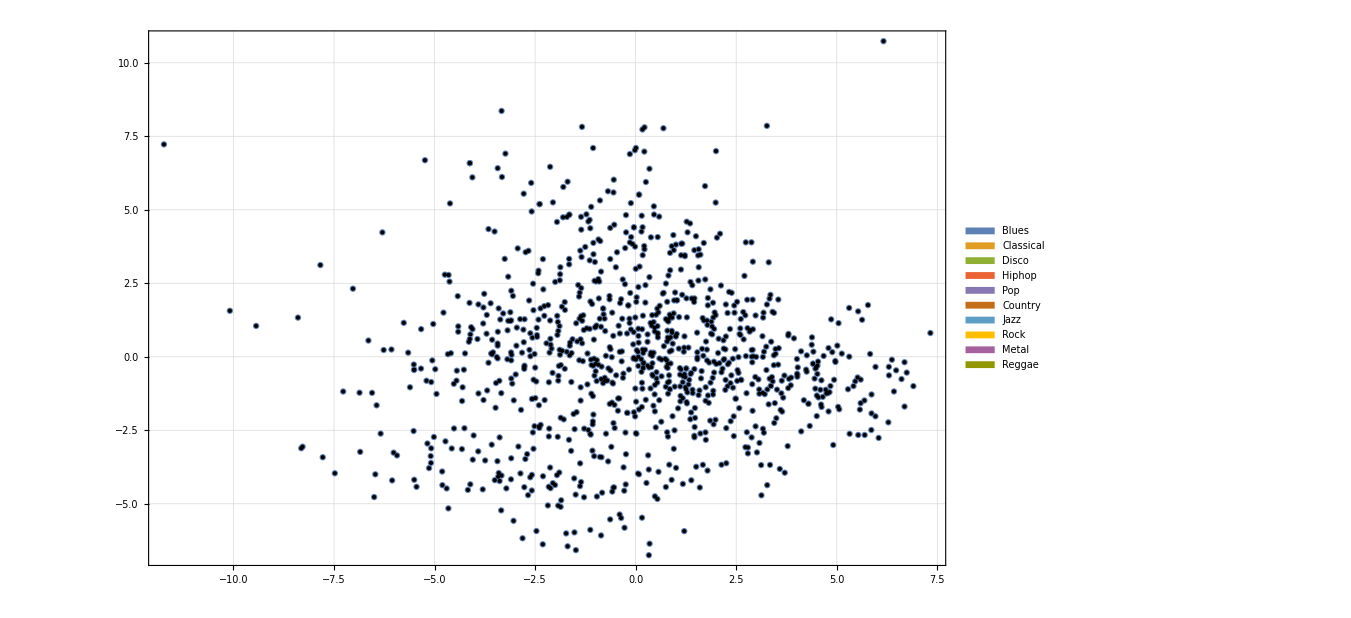

```mathematica
dr=DimensionReduce[original[[All,Values]],Method->"PrincipalComponentsAnalysis"];  (*Doing Principal Components Analysis of dataset*)
os=Transpose[{dr[[All,1]],dr[[All,2]],Normal[original[[All,37]]]}];                                 (*Adding the genre along with the PCA*)
ListPlot[Style[{#,#2},ColorData[97][#3],PointSize[.0075]]&@@@os,PlotTheme-> "Detailed",ImageSize-> 1000,                                                                                    (*Apply is used here to color each point according to its genre*)PlotLegends->SwatchLegend[RandomInteger[{97,107}],                                (*SwatchLegend is used make user defined legends*)Array[Switch[#,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"]&,10],LegendMarkers-> "Bubble"]]
```

The above plot shows the PCA of the dataset formed which shows the variance and standard deviation present in the data. It can be seen that very high varaince is present in the data which shows that noise is present in high quantity. The plot also shows the outlier present in the dataset.

### Data Prediction Models

For developing prediction models, different number of genres are taken for training and for testing the accuracy of prediction model. These models are trained using 10,9,8 and 7 genres separately and then accuracy in each case is recorded in a dataset.
This method is done because some Genres are very similar and to remove that similarity, this method will find the genres that should be removed to find better prediction.

#### 10

In this case all 10 genres are taken

```mathematica
d=original;
r=RandomSample[d,250];                                                (*RandomSample is used to create test data for prediction*)
ResultModel[d,r,10,"None"];
```

#### 9

In this case 9 genres are taken and models are trained  10 times removing one genre each time

```mathematica
Do[d=original[Select[#Genre≠ i&]][All,{"Genre"->(If[#==10, i,#]&)}];
r=RandomSample[d,225];
rem1=Switch[i,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
ResultModel[d,r,9,rem1];,{i,1,10,1}]
```

#### 8

In this case 8 genres are taken and models are trained 45 times removing two genres each time

```mathematica
Do[e=original[Select[#Genre≠ j&]];
Do[d=e[Select[#Genre≠ i&]];
d=d[All,{"Genre"->(If[#==9, i,#]&)}][All,{"Genre"->(If[#==10, j,#]&)}];
r=RandomSample[d,200];
rem1=Switch[i,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
rem2=Switch[j,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
ResultModel[d,r,8,{rem1,rem2}];,{i,j-1,1,-1}],{j,10,2,-1}]
```

#### 7

In this case 7 genres are taken and models are trained 120 times removing three genres each time

```mathematica
Do[e=original[Select[#Genre≠ k&]];
Do[b=e[Select[#Genre≠ j&]];
Do[d=b[Select[#Genre≠ i&]];
d=d[All,{"Genre"->(If[#==8, i,#]&)}][All,{"Genre"->(If[#==9, j,#]&)}][All,{"Genre"->(If[#==10, k,#]&)}];
r=RandomSample[d,175];
rem1=Switch[i,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
rem2=Switch[j,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
rem3=Switch[k,1,"Blues",2,"Classical",3,"Disco",4,"Hiphop",5,"Pop",6,"Country",7,"Jazz",8,"Rock",9,"Metal",10,"Reggae"];
ResultModel[d,r,7,{rem1,rem2,rem3}];
,{i,j-1,1,-1}],{j,k-1,2,-1}],{k,10,3,-1}]
```

## Result Analysis

### Result Dataset

The result list converts into dataset and then two columns are added containing the best accuracy of using that genre case and the respective machine learning model . The data is shown below.
It contains 176 total cases of different genres selected and different number of genres selected

```mathematica
Result=Dataset[res];
Result=Result[All,<|#,"Max"->Max[#DecisionTree,#GradientBoostedTrees,#LinearRegression,#NearestNeighbors,#NeuralNetwork,#RandomForest,#GaussianProcess],"Predictor"-> PositionIndex[#][Max[#DecisionTree,#GradientBoostedTrees,#LinearRegression,#NearestNeighbors,#NeuralNetwork,#RandomForest,#GaussianProcess]][[-1]]|>&]
```

Dataset[<>]

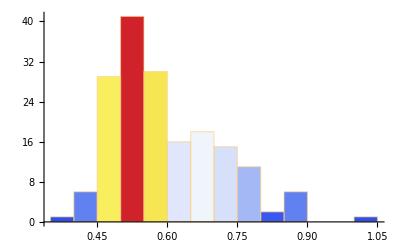

```mathematica
Histogram[Result[[All,"Max"]],ColorFunction->"TemperatureMap"]
```

In the above graph it can be seen that most of the cases shows maximum efficiency in range of 50-55%.  Majority of the cases shows result in the range of 45-60%. It gives us a general idea how our dataset has noisy data which has decreased our efficiency. In cases which has reduced the noisy data has shown better efficiency compared to others and increased to 80+%.

### Best Machine Learning Models

In the following  table and pie chart it can be seen how many times each predictor method has been selected as best method.

```mathematica
Tally[Result[[All,"Predictor"]]]
PieChart3D[Normal[Tally[Result[[All,"Predictor"]]][[All,2]]],ChartLegends->Normal[Tally[Result[[All,"Predictor"]]][[All,1]]],ImageSize->Large]
```

Dataset[<>]

-Graphics3D-

It has shown the best three model have been chosen much more times than others which means they have provided maximum accuracy in most cases. 
The Following three best machine learning model which has shown best prediction overall are shown into the list.

```mathematica
BestPred=Normal[Keys[ReverseSortBy[Counts[Result[All,"Predictor"]],Total]][1;;3]]
```

{NearestNeighbors,DecisionTree,GradientBoostedTrees}

These machine learning methods shown best result because as we know the dataset contains similar genre and thus creating noisy data. Hence methods which train the model very precisely according to the data like Random Forest and Neural Network will also train on the noisy data thus creating more incorrect output. Models like linear regression or Gaussian Process will not train the model properly due to large amount of data.
The following graph is showing how well all three models are performing for best 50 overall cases.

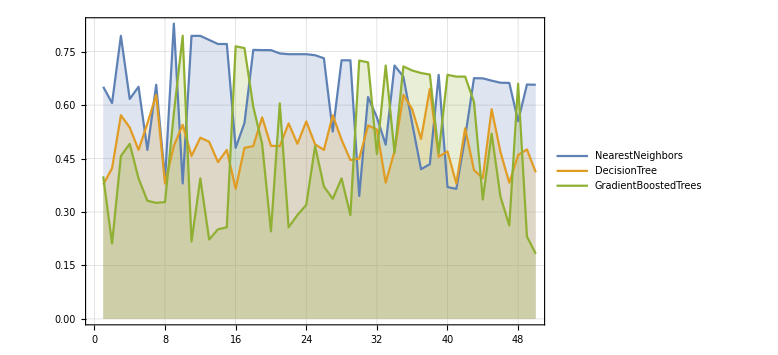

```mathematica
x=Result[TakeLargestBy["Max",50]][[All,BestPred[[1]]]];
y=Result[TakeLargestBy["Max",50]][[All,BestPred[[2]]]];
z=Result[TakeLargestBy["Max",50]][[All,BestPred[[3]]]];
ListLinePlot[{x,y,z},PlotTheme->"Detailed",Filling->Axis,Axes-> True,PlotLegends->{BestPred[[1]],BestPred[[2]],BestPred[[3]]},ImageSize->Large]
```

### Best Genres

The following dataset shows best 5 cases of genres which has given the maximum accuracy at predicting the genre of test data. It shows how many  genres are to be taken for training the model and which genres should be removed from initial 10 genres for training the model.

```mathematica
MaxAcc=Result[TakeLargestBy["Max",5]][[All,All]]
```

Dataset[<>]

Dataset[<>]

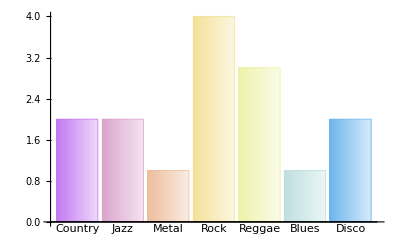

```mathematica
gen=Counts[Flatten[MaxAcc[[All,"Removed"]]]]
BarChart[gen,ChartStyle->"Pastel",ChartElementFunction->"FadingRectangle",ChartLabels->Automatic]
```

The above BarChart shows that the genres with high count should be removed to get better efficiency.

## Predict your own Audio

Enter the file-path of the audio whose genre you want to predict.

Disco is the best predicted Genre of the given audio file

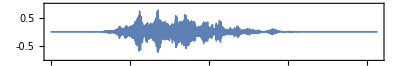

```mathematica
PredictGenre[ExampleData[{"Audio","Laughing"},"FilePath"]]
```

## Bibliography

Dataset- http://marsyas.info/downloads/datasets.html

https://towardsdatascience.com/decision-trees-in-machine-learning-641b9c4e8052

https://towardsdatascience.com/understanding-random-forest-58381e0602d2

https://towardsdatascience.com/understanding-gradient-boosting-machines-9be756fe76ab

https://towardsdatascience.com/an-intuitive-guide-to-gaussian-processes-ec2f0b45c71d

https://towardsdatascience.com/understanding-neural-networks-19020b758230

https://towardsdatascience.com/machine-learning-basics-with-the-k-nearest-neighbors-algorithm-6a6e71d01761

https://towardsdatascience.com/linear-regression-detailed-view-ea73175f6e86

As the whole set of  audio files is around 1.4 GB big, I am including the dataset on brightspace with 75 songs from each genre and the following Google Drive link will contain the whole dataset with 1000 audio files whole along with copy of Mathematica notebook.

https://drive.google.com/open?id=1U-MKJqnSkZmVNUFq4zlb4OQ8j3rh-54w

I have also attached the dataset.csv which already has the numeric valued dataset to check the project. This way there is no need to download whole audio to run the project.